```mathematica
Clear["Global`*"]
```

# Tour de TNB

## Katherine Best

104773239 
Recitation 243

## Kathryn Gray

## Amelia Westerdale

104233232
Recitation 242

### Question 1

```mathematica
x[t_]=2.9*Cos[3.2*π*t];
y[t_]=Sin[4π*t]+5t;
```

r[t] is a parametric function of the path the riders will take in the Tour de TNB race. r[t] is a vector function in 2D space such that r[t] is the position function of the riders in the race.

```mathematica
r[t_]={x[t],y[t]};
```

```mathematica
parametricplot=ParametricPlot[r[t],{t,0,1}];
```

The locations of Chateau de Cauchy and Chateau de Laplace on the parametric plot of r[t]:

```mathematica
cauchy = Graphics[{Red, Disk[{x[0],y[0]},0.1]}];
laplace = Graphics[{Blue, Disk[{x[1],y[1]},0.1]}];
cauchylabel=Graphics[Text[Style["Chateau de Cauchy",Medium,Red],{2,-0.5}]];
laplacelabel=Graphics[Text[Style["Chateau de Laplace",Medium,Blue],{-2,5.5}]];
```

```mathematica
Show[parametricplot,cauchy,laplace,cauchylabel,laplacelabel,PlotRange->All];
```

This blue text denotes the work that was done in order to find the location of the pont:

```mathematica
(* guess = Graphics[{Green, Disk[{x[0.15],y[0.15]},0.1]}]; *)
```

```mathematica
(* Show[parametricplot,cauchy,laplace,cauchylabel,laplacelabel,guess,PlotRange->All]; *)
```

FindRoot was used to find the values of time where the parametric plot intersected itself. t=a and t=b is where the pont is located.

```mathematica
FindRoot[{x[a]==x[b],y[a]==y[b]},{a,0.5},{b,0.15}]
```

{a→0.451682,b→0.173318}

```mathematica
pont=Graphics[{Green, Disk[{x[0.17331841854634955],y[0.17331841854634955]},0.1]}];
```

```mathematica
pontlabel=Graphics[Text[Style["Pont",Medium,Green],{-1,2.1}]];
```

```mathematica
turn1label=Graphics[Text[Style["Turn 1",Medium,Purple],{-2.9,0.5}]];
turn2label=Graphics[Text[Style["Turn 2",Medium,Purple],{3.0,4.4}]];
turn3label=Graphics[Text[Style["Turn 3",Medium,Purple],{-2.6,3.0}]];
```

The following plot shows the visual representation of the path the riders will take, where Chateau de Cauchy is located at t=0, where Chateau de Laplace is located at t=1, and where the pont is located at t=a and t=b.

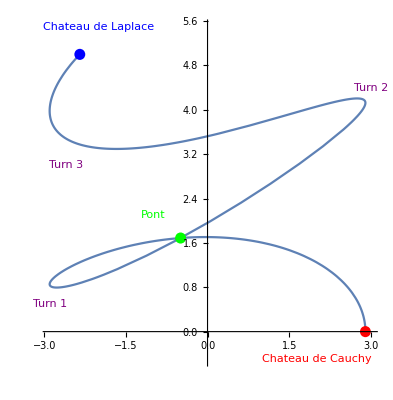

```mathematica
Show[parametricplot,cauchy,laplace,cauchylabel,laplacelabel,pont,pontlabel,turn1label,turn2label,turn3label, PlotRange->All]
```

### Question 2

Here, the speed as a function of time was calculated. Speed is a scalar function, not a vector function. Then the speed of the riders along the path r[t] was made into a plot from 0≤t≤1.

```mathematica
Speed[t_]=Sqrt[x'[t]^2+y'[t]^2]
```

√((5+4 π Cos[4 π t])^2+849.955 Sin[10.0531 t]^2)

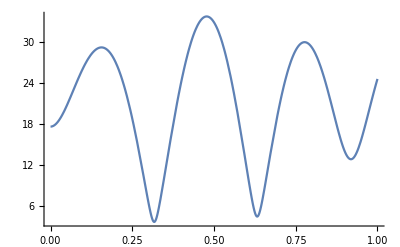

```mathematica
Plot[Speed[t],{t,0,1}]
```

The average speed along the route:
average speed is the total distance (the arc-length of the route) divided by the total time traveled, which is 1 hour.

```mathematica
aveSpeed=NIntegrate[Speed[t],{t,0,1}]/1
```

21.0979

Thus the average speed is 21.0979 km/h

### Question 3

The following calculation is the arc-length of the route.

```mathematica
NIntegrate[Speed[t],{t,0,1}]
```

21.0979

The arc-length is 21.0979 km.

The following calculation is the direct distance from Chateau de Cauchy to Chateau de Laplace as the crow flies.

```mathematica
d=√((r[0]-r[1]).(r[0]-r[1]))
```

7.24721

The direct distance is 7.24721 km.

### Question 4

```mathematica
Distance[t_] = Sqrt[x'[t]^2+y'[t]^2]
```

√((5+4 π Cos[4 π t])^2+849.955 Sin[10.0531 t]^2)

```mathematica
DistanceFromChaucy[time_?NumericQ]:=NIntegrate[Distance[t],{t,0,time}]
```

```mathematica
FindRoot[DistanceFromChaucy[time]==1,{time,0}]
```

{time→0.0531995}

```mathematica
TotalLength=NIntegrate[Distance[t],{t,0,1}];
```

```mathematica
DistanceFromLaPlace [time_?NumericQ]:=TotalLength-NIntegrate[Distance[t],{t,0,time}]
```

```mathematica
FindRoot[DistanceFromLaPlace[time]==1,{time,0.7}]
```

{time→0.950194}

### Question 5

The following calculations will find the curvature of the route as a function of time from 0≤t≤1.

```mathematica
rPrime[t_]={x'[t],y'[t],0}
```

{-29.154 Sin[10.0531 t],5+4 π Cos[4 π t],0}

```mathematica
r2prime[t_]={x''[t],y''[t],0}
```

{-293.088 Cos[10.0531 t],-16 π^2 Sin[4 π t],0}

```mathematica
Curverature[t_]=(√((rPrime[t]×r2prime[t]).(rPrime[t]×r2prime[t])))/((Speed[t])^3)
```

(√(0.+(1465.44 Cos[10.0531 t]+3683.05 Cos[10.0531 t] Cos[4 π t]+4603.81 Sin[10.0531 t] Sin[4 π t])^2))/((5+4 π Cos[4 π t])^2+849.955 Sin[10.0531 t]^2)^(3/2)

The following plot is the plot of curvature as a function of time.

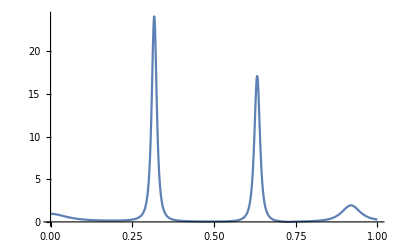

```mathematica
Plot[Curverature[t],{t,0,1},PlotRange->Full]
```

The plot of the curvature shows how the direction of the path the bikers are on changes.  The places where the curvature is greatest show where the direction changes most rapidly.

The times that have the highest curvature have the lowest speeds.  This is because the riders are required to slow down in order to maintain control over their bicycles for the tight turns.

### Question 6

Finding the maximum normal acceleration (a_N) in the domain 0≤t≤1

```mathematica
accelNormal[t_]=(Curverature[t])*((Speed[t])^2)(* Subscript[a, n]=κ|v|^2 *)
```

(√(0.+(1465.44 Cos[10.0531 t]+3683.05 Cos[10.0531 t] Cos[4 π t]+4603.81 Sin[10.0531 t] Sin[4 π t])^2))/(√((5+4 π Cos[4 π t])^2+849.955 Sin[10.0531 t]^2))

This is the plot of the normal component of acceleration (a scalar value) as a function of time.

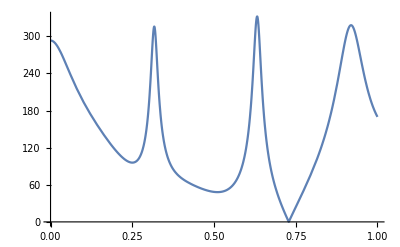

```mathematica
accelPlot = Plot[accelNormal[t],{t,0,1}]
```

When a_N is compared to the plot of the curvature, it can be seen that the peaks of the curvature plot and the a_N plot are at relatively the same times. 
When a_N is compared to the plot of speed as a function of time, it can be seen that the points of highest normal acceleration have the lowest speeds.

The normal component of the acceleration describes when the racers will be making turns and when they will have to slow down or speed up. Points on the route with sharp turns have a large a_N component, that means the riders will have to slow down. Segments of the route with little curvature have small a_N components.

The point of maximum curvature does not occur at the point of maximum a_N. In the route, there are relatively three sharp turns; the turn near the pont (the sharpest turn), the middle turn (the second sharpest turn), and the turn near the finish line (the third sharpest turn). The largest value for a_N occurs at the second sharpest turn rather than the first sharpest turn because the riders have the straightest path in between turn 1 and turn 2, so the riders will have to slow down the most for turn 2. Before the riders encounter turn 1, they are already going relatively slow since the route is curvy from Chateau de Cauchy to the first turn, so less a_N is required from the riders.

### Question 7

```mathematica
FindMaximum[accelNormal[t],{t,0.63}]
```

{331.98,{t→0.631983}}

```mathematica
accelGraphics=Graphics[{PointSize[0.02],Point[{0.6319831262838493,331.9800398365562}]}];
```

The following graph is a depiction of the normal acceleration (a scalar value) as a function of time from 0≤t≤1.

The black point on the normal acceleration plot denotes the location of where the largest normal acceleration occurs from 0≤t≤1.

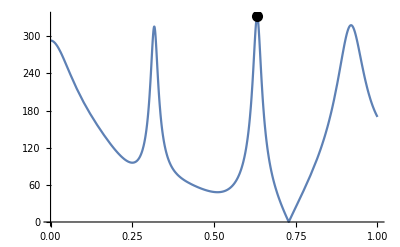

```mathematica
Show[accelPlot, accelGraphics,PlotRange->All]
```

The hay bales should be placed on the route at t=0.31728 hours.

The hay bales should go at the places with the largest normal acceleration because these are the places where the riders are required to turn the sharpest.  If they do not turn sharp enough, that is , if they do not have enough normal acceleration, then they are more likely to go off the side of the course, so the hay bales should be placed where the turns that are the hardest to make are so that if the riders do not provide the normal acceleration required to make the turn they are protected by the hay bales.

### Question 8

```mathematica
TimeForFood=6/60;
Func[m_]=Integrate[Curverature[t],{t,m,m+TimeForFood}]
```

∫_m^(1/10+m) ((√(0.+(1465.44 Cos[10.0531 t]+3683.05 Cos[10.0531 t] Cos[4 π t]+4603.81 Sin[10.0531 t] Sin[4 π t])^2))/((5+4 π Cos[4 π t])^2+849.955 Sin[10.0531 t]^2)^(3/2))ⅆt

```mathematica
FindMinimum[D[Func[m],m]==0,{m,0.5}]
```